```mathematica
δ = 0.29;
ω =0.73;
rozw = DSolve[{x''[t]+ 2δ  x'[t]+ω^2x[t]==0, x[0]== 100, x'[0] == 0},x[t], {t, 0, 50}];
rozw2 = DSolve[{x2''[t]+ 2δ  x2'[t]+ω^2x2[t]==0, x2[0] == 0, x2'[0] == 100},x2[t], {t, 0, 50}]
```

{{x2[t]→149.27 ⅇ^(-0.29 t) Sin[0.669925 t]}}

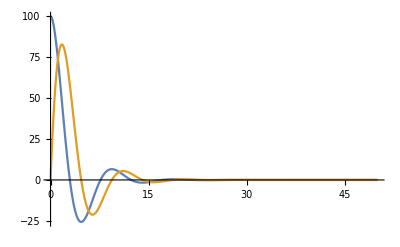

```mathematica
Plot[{x[t]/.rozw, x2[t]/.rozw2}, {t, 0, 50}, PlotRange->All]
```